```mathematica
ApplyToGraph[g_Graph,sets_List]:=Block[{result=g, labels,colors=Association[ToColors2[sets]],indexes=Association[]},
labels=AnnotationValue[g,"VertexLabels"];
If [FailureQ[labels],
labels=Map[#->Style[#,colors[#]]&,VertexList[g]];
Table[indexes[v]={If[KeyExistsQ[colors,v],Style[v,colors[v], Bold],v]},{v,VertexList[g]}]
];
labels=Association[labels];
Table[
If[Length[bucket]≠1,
indexes[bucket[[1]]]=Flatten[{indexes[bucket[[1]]],indexes[bucket[[2]]]}];
labels[bucket[[1]]]=ToString[labels[bucket[[1]]]]<>", " <> ToString[bucket[[2]]];
labels=KeyDrop[labels,bucket[[2]]];
result=Graph[VertexContract[result,bucket]]
],
{bucket,sets}
];
Table[If[Length[indexes[k]]>1,indexes[k]=Row[indexes[k],", "]],
{k,Keys[indexes]}];
Graph[result,VertexLabels->Normal[indexes]]
]
```

```mathematica
ToColors2[buckets_]:=Block[{index,  color,  result},
result={};
For[index=1,index≤Length[buckets],index++,
color= IndexToColor [index ];
Table[AppendTo[result,node->color],
{node,buckets[[index]]}];
];
result
]
```

```mathematica
ZykovDecomposition3[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta,g2},
g2=Graph[g,VertexLabels->Map[#->#&,VertexList[g]]];
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g2,split[[1]]];
right=VertexDelete[g2,split[[2]]];
middle=VertexDelete[g2,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
Column[
{GraphWithChrom2[Graph[EdgeList[g2],GraphHighlight->EdgeList[CycleGr[vertices]],GraphHighlightStyle->"Thick", GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->400]],
Multicolumn[Map[SymbolToGraph,Sort[FindFullFormula[middle],SymbolComp3]]//Reverse],
TableForm[
Monitor[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
{Rotate[SetsToLabel[sol],Pi/2],
GraphWithChrom2[lefta]*GraphWithChrom2[righta]/GraphWithChrom2[middlea]->(Factor[(Framed[ChromaticPolynomial[lefta,4]]*Framed[ChromaticPolynomial[righta,4]]/Framed[ChromaticPolynomial[middlea,4]])])
},
{sol,Select[sols,Length[#]<=4&]}
],
sol]
]
}
]
]
```

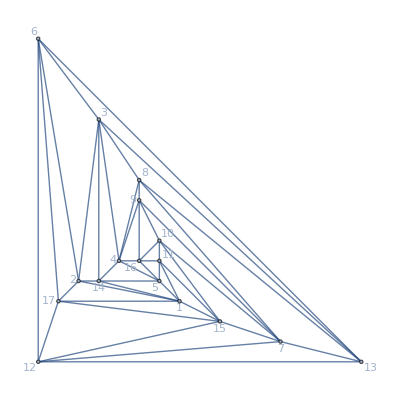
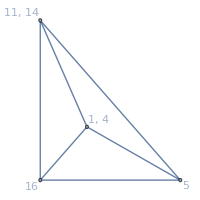
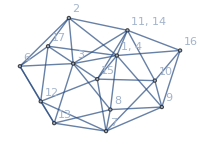
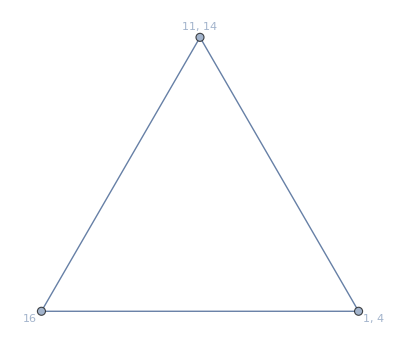
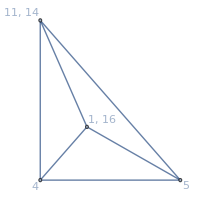
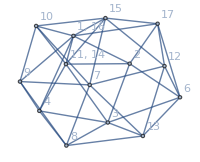
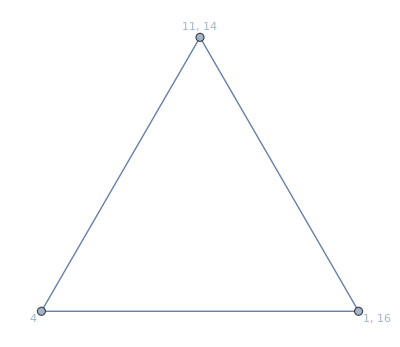
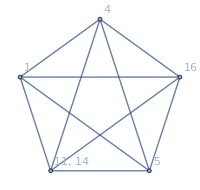
-Graphics-{528}
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
14♁be♁g | (-Graphics-{24} -Graphics-{96})/(-Graphics-{24})→96
1g♁4♁be | (-Graphics-{24} -Graphics-{48})/(-Graphics-{24})→48
1♁4♁be♁g | (-Graphics-{0} -Graphics-{168})/(-Graphics-{24})→(0 168)/24
1g♁4b♁e | (-Graphics-{24} -Graphics-{72})/(-Graphics-{24})→72
1♁4b♁eg | (-Graphics-{24} -Graphics-{144})/(-Graphics-{24})→144
1♁4b♁e♁g | (-Graphics-{0} -Graphics-{192})/(-Graphics-{24})→(0 192)/24
14♁b♁eg | (-Graphics-{24} -Graphics-{168})/(-Graphics-{24})→168
14♁b♁e♁g | (-Graphics-{0} -Graphics-{216})/(-Graphics-{24})→(0 216)/24
1g♁4♁b♁e | (-Graphics-{0} -Graphics-{168})/(-Graphics-{24})→(0 168)/24
1♁4♁b♁eg | (-Graphics-{0} -Graphics-{240})/(-Graphics-{24})→(0 240)/24

```mathematica
ZykovDecomposition3[plantri8,{1,14,4,16,11}]
```

```mathematica
ApplyToGraphEmpty[g_Graph,sets_List]:=Block[{result=g, labels,edge},
labels=AnnotationValue[g,"VertexLabels"];
If [FailureQ[labels],
labels=Map[#->#&,VertexList[g]]
];
labels=Association[labels];
Table[
edge=UndirectedEdge[pair[[1]],pair[[2]]];
If[EdgeQ[result,edge],result=EdgeDelete[result,edge]],
{pair,Subsets[Flatten[sets],{2}]}];
Table[
If[Length[bucket]≠1,
labels[bucket[[1]]]=ToString[labels[bucket[[1]]]]<>", " <> ToString[bucket[[2]]];
labels=KeyDrop[labels,bucket[[2]]];
result=Graph[VertexContract[result,bucket],VertexLabels->Normal[labels]]
],
{bucket,sets}
];
result
]
```

```mathematica
FindEmptyFormula2[g_]:=Block[{},
Monitor[
formulaDepth=0;FindEmptyFormula2[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindEmptyFormula2[g_,v_]:=Block[{edge,pos1,pos2,v2,result=0},
If[EmptyGraphQ[g],
(* ok : done *)
result=SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&],"n"]
,
(* else *)
edge=First[EdgeList[g]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=FindEmptyFormula2[EdgeDelete[g,edge],v]-
FindEmptyFormula2[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

```mathematica
SymbolToGraphEmpty[s_]:=Block[{blocks=SymbolToSets[s]},
Graph[Range[Length[blocks]],{},VertexLabels->Table[k->If[Length[blocks[[k]]]==1,ToString[blocks[[k,1]]],StringRiffle[Map[ToString,blocks[[k]]],", "]],{k,Length[blocks]}], ImageSize->{60,60}, VertexStyle->Red, VertexLabelStyle->Darker[Green],  VertexSize->Small]
]
```

```mathematica
ZykovDecompositionEmpty[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta,g2,formula, repEmpty={}},
g2=Graph[g,VertexLabels->Map[#->#&,VertexList[g]]];
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g2,split[[1]]];
right=VertexDelete[g2,split[[2]]];
middle=VertexDelete[g2,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
Print[middle];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
formula=FindEmptyFormula2[middle];
sols=Map[SymbolToSets,ListofVars[formula]]//Reverse;
Column[
{GraphWithChrom2[Graph[EdgeList[g2],GraphHighlight->EdgeList[CycleGr[vertices]],GraphHighlightStyle->"Thick", GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->400]],
formula,
TableForm[
Monitor[
Table[
middlea=ApplyToGraphEmpty[middle2,sol];
lefta=Graph[ApplyToGraphEmpty[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraphEmpty[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
{Rotate[SetsToLabel[sol],Pi/2],
AppendTo[repEmpty,SetsToSymbol[sol,"n"]->(ChromaticPolynomial[lefta,4]*ChromaticPolynomial[righta,4]/ChromaticPolynomial[middlea,4])];
Print[repEmpty];
Print[formula/.repEmpty];
GraphWithChrom2[lefta]*GraphWithChrom2[righta]/GraphWithChrom2[middlea]->(Factor[(Framed[ChromaticPolynomial[lefta,4]]*Framed[ChromaticPolynomial[righta,4]]/Framed[ChromaticPolynomial[middlea,4]])])
},
{sol,sols}
],
sol]
]
}
]
]
```

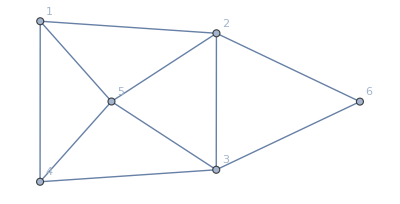

```mathematica
g
```

```mathematica
ConnectedComponents[VertexDelete[g,{1,2,3,4}]]
```

{{5},{6}}

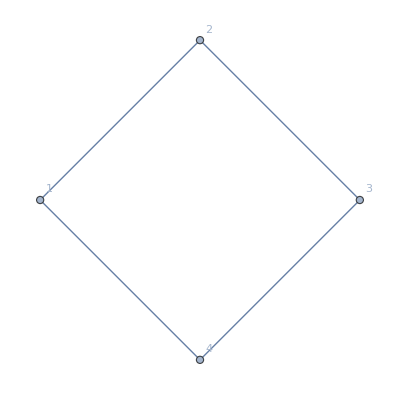

{n1x2x34→243}

-243-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4+n1x2x3x4

{n1x2x34→243,n1x23x4→324}

-567-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234+n1x2x3x4

{n1x2x34→243,n1x23x4→324,n14x2x3→243}

-810-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23+n1x234+n1x2x3x4

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243}

-1053-3 n1234+n123x4+n124x3+n12x34+n134x2+n14x23+n1x234+n1x2x3x4

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243,n1234→36}

-1161+n123x4+n124x3+n12x34+n134x2+n14x23+n1x234+n1x2x3x4

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243,n1234→36,n1x2x3x4→729}

-432+n123x4+n124x3+n12x34+n134x2+n14x23+n1x234

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243,n1234→36,n1x2x3x4→729,n1x234→108}

-324+n123x4+n124x3+n12x34+n134x2+n14x23

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243,n1234→36,n1x2x3x4→729,n1x234→108,n14x23→108}

-216+n123x4+n124x3+n12x34+n134x2

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243,n1234→36,n1x2x3x4→729,n1x234→108,n14x23→108,n134x2→81}

-135+n123x4+n124x3+n12x34

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243,n1234→36,n1x2x3x4→729,n1x234→108,n14x23→108,n134x2→81,n12x34→81}

-54+n123x4+n124x3

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243,n1234→36,n1x2x3x4→729,n1x234→108,n14x23→108,n134x2→81,n12x34→81,n124x3→81}

27+n123x4

{n1x2x34→243,n1x23x4→324,n14x2x3→243,n12x3x4→243,n1234→36,n1x2x3x4→729,n1x234→108,n14x23→108,n134x2→81,n12x34→81,n124x3→81,n123x4→108}

135

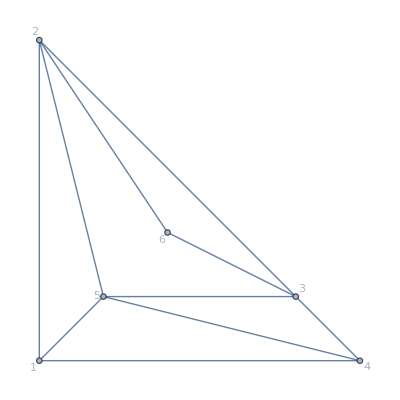
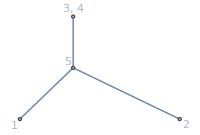
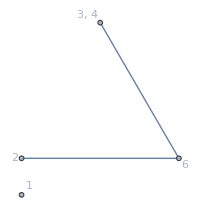
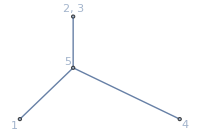
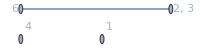
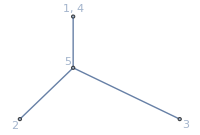
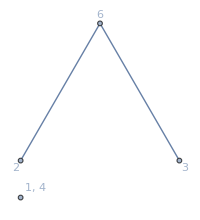
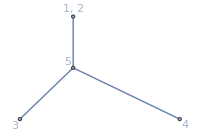
-Graphics-{144}
-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4
1♁2♁34 | (-Graphics-{108} -Graphics-{144})/(-Graphics-{64})→(108 144)/64
1♁23♁4 | (-Graphics-{108} -Graphics-{192})/(-Graphics-{64})→(108 192)/64
14♁2♁3 | (-Graphics-{108} -Graphics-{144})/(-Graphics-{64})→(108 144)/64
12♁3♁4 | (-Graphics-{108} -Graphics-{144})/(-Graphics-{64})→(108 144)/64
1234 | (-Graphics-{12} -Graphics-{12})/(-Graphics-{4})→12^2/4
1♁2♁3♁4 | (-Graphics-{324} -Graphics-{576})/(-Graphics-{256})→(324 576)/256
1♁234 | (-Graphics-{36} -Graphics-{48})/(-Graphics-{16})→(36 48)/16
14♁23 | (-Graphics-{36} -Graphics-{48})/(-Graphics-{16})→(36 48)/16
134♁2 | (-Graphics-{36} -Graphics-{36})/(-Graphics-{16})→36^2/16
12♁34 | (-Graphics-{36} -Graphics-{36})/(-Graphics-{16})→36^2/16
124♁3 | (-Graphics-{36} -Graphics-{36})/(-Graphics-{16})→36^2/16
123♁4 | (-Graphics-{36} -Graphics-{48})/(-Graphics-{16})→(36 48)/16

```mathematica
ZykovDecompositionEmpty[g,{1,2,3,4}]
```

```mathematica
Graph[{1,2,3,4},{},VertexLabels->{1->"1",2->"2",3->"3",4->"4"}]
```

-Graphics-